## Adaptive dynamics models

### Logistic growth model

#### Evolution of birth rate

What we are asking here is whether a mutant host with a different birth rate could invade when the resident host is at its carrying capacity. We assume that death rate is a linear function of the birth rate Mathematically, this is equivalent to asking whether the Jacobian matrix, evaluated at the mutant-free equilibrium, has at least one positive eigenvalue.

```mathematica
(* This is the model *)
dR=b (1-(R+Rm)/K) R-d[b] (1-(R+Rm)/K) R;
dRm=bm (1-(R+Rm)/K) Rm-d[bm] (1-(R+Rm)/K) Rm;
(* The Jacobian *)
MatrixForm[J=D[{dR,dRm},{{R,Rm}}]]
```

(-(b R)/K+b (1-(R+Rm)/K)+(R d[b])/K-(1-(R+Rm)/K) d[b] | -(b R)/K+(R d[b])/K
-(bm Rm)/K+(Rm d[bm])/K | -(bm Rm)/K+bm (1-(R+Rm)/K)+(Rm d[bm])/K-(1-(R+Rm)/K) d[bm])

```mathematica
(* The Jacobian, evaluated at the mutant-free equilibrium *)
MatrixForm[J=D[{dR,dRm},{{R,Rm}}]/.{R->K,Rm->0}]
```

(-b+d[b] | -b+d[b]
0 | 0)

```mathematica
(* Eigenvalues are *)
Eigenvalues[J]
```

{-b+d[b],0}

Based on this, it is clear that -b+d < 0, which is necessary for the resident to be able to exist at all. The 0 eigenvalue implies that the system is neutrally stable, and no evolution will happen in this system.

### Alternative logistic growth model

#### Evolution of birth rate

Here I assume that d is a function of b (keeping it unspecified for the moment).

```mathematica
(* This is the model *)
dR=(b-bs (R+Rm)) R-(d[b]+ds (R+Rm))R;
dRm=(bm-bs (R+Rm)) Rm-(d[bm]+ds (R+Rm))Rm;
(* The Jacobian *)
MatrixForm[J=D[{dR,dRm},{{R,Rm}}]]//Simplify
```

(b-(bs+ds) (2 R+Rm)-d[b] | -(bs+ds) R
-(bs+ds) Rm | bm-(bs+ds) (R+2 Rm)-d[bm])

```mathematica
(* The Jacobian, evaluated at the mutant-free equilibrium *)
Solve[(dR/.Rm->0)==0,R]
MatrixForm[J=D[{dR,dRm},{{R,Rm}}]/.{R->(b-d[b])/(bs+ds),Rm->0}]
```

{{R→0},{R→(b-d[b])/(bs+ds)}}

(b-(2 bs (b-d[b]))/(bs+ds)-(2 ds (b-d[b]))/(bs+ds)-d[b] | -(bs (b-d[b]))/(bs+ds)-(ds (b-d[b]))/(bs+ds)
0 | bm-(bs (b-d[b]))/(bs+ds)-(ds (b-d[b]))/(bs+ds)-d[bm])

```mathematica
(* Eigenvalues are *)
Eigenvalues[J]//Simplify
```

{-b+d[b],-b+bm+d[b]-d[bm]}

The invasion fitness is b_m-b+d(b)-d(b_m). Notice that if b_m>b, then d(b_m)>d(b) suggesting that the invasion fitness may not always be positive. As such, there are more possibilities for evolution in this system.

The fitness gradient bear this out. It is 1-d'(b); since d'(b)> 0, the fitness gradient may be positive or negative, depending on whether, at the current b, d'(b)<1 or not. In this case, there will be a singular strategy (an endpoint of evolution) when d'(b)=1. In other words, evolution will continue until b satisfies this condition. Notice that a linear function will never be able to satisfy this condition - d(b) is linear then d'(b) will be a constant that will either be larger or smaller than 1, and evolution will either drive b to zero or to infinity, respectively.

```mathematica
D[Eigenvalues[J][[2]],bm]/.bm->b
```

1-d'[b]

However, if d(b) is nonlinear, then singular strategies are possible. Whether any singular strategy represents an evolutionarily stable strategy (a fitness maximum) depends on the second derivative of the fitness gradient with respect to the evolving trait, evaluated at the singular strategy. (I.e., it is the curvature of the fitness gradient; if the second derivative is negative, the fitness gradient is at a peak.) This ESS condition is -d''(b), meaning that d''(b)>0 for there to be an evolutionarily stable strategy (i.e., death rate must be accelerating function of birth rate).

```mathematica
D[Eigenvalues[J][[2]],{bm,2}]/.bm->b
```

-d''[b]

Here’s a numerical example, just to make this a bit more concrete, and to potentially give you something to push back against with the GEM.

If d(b)=d_0 b^2, with d_0=1/6, then the evolutionarily stable b value will be:

```mathematica
Solve[2 d0 b==1,b]
Solve[2 d0 b==1,b]/.d0->1/6
```

{{b→1/(2 d0)}}

{{b→3}}

The carrying capacity at this evolutionarily stable b value (assuming b_slope=d_slope=1/6 is 12.5.

```mathematica
Solve[(b-bs (R)) R-(d[b]+ds (R))R==0,R][[2]]/.{d[b]->d0 b^2}/.{b->1/(2 d0)}/.{d0->1/6,bs->0.1,ds->0.1}
```

{R→7.5}

Question: what happens when you simulate the system of resident and mutant? Can the mutant actually invade and displace the resident?

```mathematica
Solve[(dR/.{Rm->0}/.{d[b]->d0 b}/.{b->1,d0->1/6,bs->0.1,ds->0.1})==0,R]
```

{{R→0.},{R→4.16667}}

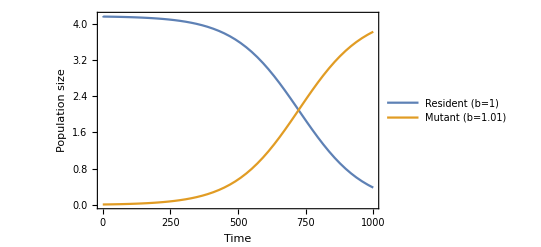

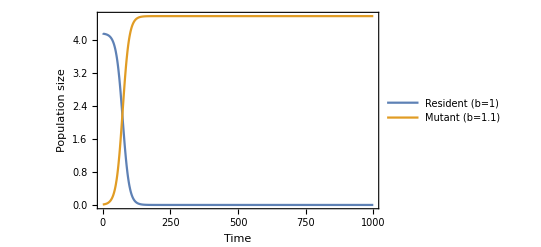

```mathematica
sol=NDSolve[{R'[t]==(dR/.{R->R[t],Rm->Rm[t]}/.{d[b]->d0 b}/.{b->1,d0->1/6,bs->0.1,ds->0.1}),
Rm'[t]==(dRm/.{R->R[t],Rm->Rm[t]}/.{d[bm]->d0 bm}/.{bm->1.01,d0->1/6,bs->0.1,ds->0.1}),
R[0]==4.166666666666667,Rm[0]==0.01},{R,Rm},{t,0,1000}];
Plot[{R[t]/.sol,Rm[t]/.sol},{t,0,1000}, Frame->True,FrameLabel->{"Time","Population size"},PlotLegends->Placed[LineLegend[{"Resident (b=1)","Mutant (b=1.01)"}],{0.2,0.5}]]
sol=NDSolve[{R'[t]==(dR/.{R->R[t],Rm->Rm[t]}/.{d[b]->d0 b}/.{b->1,d0->1/6,bs->0.1,ds->0.1}),
Rm'[t]==(dRm/.{R->R[t],Rm->Rm[t]}/.{d[bm]->d0 bm}/.{bm->1.1,d0->1/6,bs->0.1,ds->0.1}),
R[0]==4.166666666666667,Rm[0]==0.01},{R,Rm},{t,0,1000}];
Plot[{R[t]/.sol,Rm[t]/.sol},{t,0,1000}, Frame->True,FrameLabel->{"Time","Population size"},PlotLegends->Placed[LineLegend[{"Resident (b=1)","Mutant (b=1.1)"}],{0.7,0.5}]]
```

Question: what happens if the resident is at the ESS?

```mathematica
Solve[(dR/.{Rm->0}/.{d[b]->d0 b^2}/.{b->3,d0->1/6,bs->0.1,ds->0.1})==0,R]
```

{{R→0.+0. ⅈ},{R→7.5}}

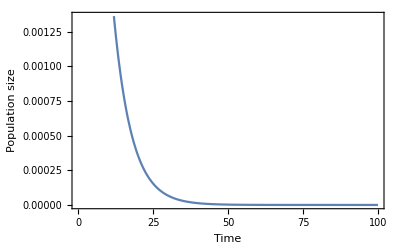

```mathematica
sol=NDSolve[{R'[t]==(dR/.{R->R[t],Rm->Rm[t]}/.{d[b]->d0 b^2}/.{b->3,d0->1/6,bs->0.1,ds->0.1}),
Rm'[t]==(dRm/.{R->R[t],Rm->Rm[t]}/.{d[bm]->d0 bm^2}/.{bm->4,d0->1/6,bs->0.1,ds->0.1}),
R[0]==7.5,Rm[0]==0.01},{R,Rm},{t,0,1000}];
Plot[{Rm[t]/.sol},{t,0,100}, Frame->True,FrameLabel->{"Time","Population size"}]
```

### Lotka-Volterra model

```mathematica
(* the model *)
dR=b R-d[b] R-a R P;
dP=e a (R+Rm) P-dp P;
dRm=bm Rm-d[bm] Rm-a Rm P;
(* the Jacobian *)
MatrixForm[J=D[{dR,dP,dRm},{{R,P,Rm}}]/.Rm->0]
```

(b-a P-d[b] | -a R | 0
a e P | -dp+a e R | a e P
0 | 0 | bm-a P-d[bm])

The mutant can invade if b_m-d(b_m)-a P̂>0. The fitness gradient is

```mathematica
D[bm-a P-d[bm],bm]
```

1-d'[bm]

Thus if d is linear function of b, evolution will lead to either infinite birth rate, or zero birth rate, depending on the slope. If d'(b_m) is nonlinear, then an ESS is possible. Assuming d(b) = d0*b^2:

```mathematica
Solve[1-D[d0 b^2,b]==0,b]/.d0->1/6
```

{{b→3}}

### Rosenzweig-MacArthur model

### S-I model

```mathematica
(* the model *)
ds=(b-bslope (s+i+sm+im)) (s+i)-d[b] s-β s (i+im);
di=β s (i+im)-(v+d[b]) i;
dsm=(bm-bslope (s+i+sm+im)) (sm+im)-d[bm] sm-β sm (i+im);
dim=β sm (i+im)-(v+d[bm]) im;
```

```mathematica
(* the Jacobian *)
MatrixForm[J=D[{ds,di,dsm,dim},{{s,i,sm,im}}]/.{sm->0,im->0}]
```

(b-2 bslope (i+s)-i β-d[b] | b-2 bslope (i+s)-s β | -bslope (i+s) | -bslope (i+s)-s β
i β | -v+s β-d[b] | 0 | s β
0 | 0 | bm-bslope (i+s)-i β-d[bm] | bm-bslope (i+s)
0 | 0 | i β | -v-d[bm])

```mathematica
F={{bm-bslope (i+s),bm-bslope (i+s)},{0,0}};
V={{i β+d[bm],0},{-β i,v+d[bm]}};
J[[3;;4,3;;4]]==F-V
invfit=Eigenvalues[F.Inverse[V]][[2]]
```

True

((-bm+bslope i+bslope s) (-v-i β-d[bm]))/((v+d[bm]) (i β+d[bm]))

```mathematica
invfit==(bm-bslope (s+i))/(d[bm]+β i)+(β i)/(d[bm]+β i)(bm-bslope (s+i))/(d[bm]+v)//Simplify
```

True

Equilibria:

```mathematica
Solve[(di/.{sm->0,im->0})==0,s]
Solve[(ds/.{sm->0,im->0})==0,i]
```

{{s→(v+d[b])/β}}

{{i→(b-2 bslope s-s β+√(b^2-2 b s β+4 bslope s^2 β+s^2 β^2-4 bslope s d[b]))/(2 bslope)},{i→-(-b+2 bslope s+s β+√(b^2-2 b s β+4 bslope s^2 β+s^2 β^2-4 bslope s d[b]))/(2 bslope)}}

```mathematica
(* Note that b-2 bslope s - sβ is equal to b-2 bslope (v+d[b])/β-(v+d[b]) *)
(* if d[b] is a linear function of b, d[b] = d0 b, then b-2 bslope (v+d[b])/β-(v+d[b]) = b-2 bslope (v+d[b])/β-v-d0 b = (1-d0) b-2 bslope (v+d[b])/β-v*)
(* which means that d0 has to be a very small number for this to be positive *)
```

```mathematica
(* If b-2 bslope s - sβ > 0 then the first equilibrium is always positive *)
(* the second equilibrium will be positive only if (-b+bslope s+d[b])>0 *)
(* however, b - 2 bslope s -β s > 0 and (-b + bslope s + d[b]) > 0 *)
(* implies b > 2 bslope s + β s and b < bslope s + d[b], which means that 2 bslope s + β s < bslope s + d[b], which is impossible because β s > d[b] *)
(* thus if b - 2 bslope s - β s > 0, the first equilibrium is the equilibrium of interest *)
b-2 bslope s-s β>√(b^2-2 b s β+4 bslope s^2 β+s^2 β^2-4 bslope s d[b]);
Simplify[Expand[(b-2 bslope s-s β)^2>b^2-2 b s β+4 bslope s^2 β+s^2 β^2-4 bslope s d[b]]]
```

bslope s (-b+bslope s+d[b])>0

```mathematica
(* If b-2 bslope s - sβ  is negative, then the second equilibrium is always negative *)
(* the first equilibrium will be positive only if (-b+bslope s+d[b]) < 0, which means that b - 2 bslope s - s β < 0 and b - bslope s - d[b] > 0; this must be true because b - bslope s -d[b] is the per-capita growth rate of the susceptible population when there are no infections; with infections this must be true *)
(* thus if b - 2 bslope s - β s < 0, the first equilibrium is the equilibrium of interest *)

(* thus, we know that the first equilibrium is always the correct one, regardless of the sign of b-2 bslope 2-s β *)
b-2 bslope s-s β+√(b^2-2 b s β+4 bslope s^2 β+s^2 β^2-4 bslope s d[b])>0;
√(b^2-2 b s β+4 bslope s^2 β+s^2 β^2-4 bslope s d[b])>-(b-2 bslope s-s β);
Simplify[Expand[b^2-2 b s β+4 bslope s^2 β+s^2 β^2-4 bslope s d[b]>(-(b-2 bslope s-s β))^2]]
```

bslope s (-b+bslope s+d[b])<0

```mathematica
Simplify[D[invfit,bm]]
```

1/((v+d[bm])^2 (i β+d[bm])^2)(i v β (v+i β)+d[bm]^3-(bm-bslope (i+s)) (v^2+i v β+i^2 β^2) d'[bm]+d[bm]^2 (2 (v+i β)+(-bm+bslope (i+s)) d'[bm])+d[bm] (v^2+3 i v β+i^2 β^2-2 (bm-bslope (i+s)) (v+i β) d'[bm]))

```mathematica
fitgrad=Collect[Expand[Numerator[Simplify[D[invfit,bm]]]],d'[bm]]/.bm->b
```

i v^2 β+i^2 v β^2+v^2 d[b]+3 i v β d[b]+i^2 β^2 d[b]+2 v d[b]^2+2 i β d[b]^2+d[b]^3+(-b v^2+bslope i v^2+bslope s v^2-b i v β+bslope i^2 v β+bslope i s v β-b i^2 β^2+bslope i^3 β^2+bslope i^2 s β^2-2 b v d[b]+2 bslope i v d[b]+2 bslope s v d[b]-2 b i β d[b]+2 bslope i^2 β d[b]+2 bslope i s β d[b]-b d[b]^2+bslope i d[b]^2+bslope s d[b]^2) d'[b]

```mathematica
fitgrad==(v+d[b]) (i β+d[b]) (v+i β+d[b])-(b-bslope (i+s)) ((v+i β+d[b])^2-β v i)d'[b]//Simplify
```

True

```mathematica
(* Notice that if d is a linear function of b, the fitness gradient is always positive *)
Expand[fitgrad/.{d[b]->d0 b,d'[b]->d0}]
```

b^2 bslope d0^3 i+b^2 bslope d0^3 s+2 b bslope d0^2 i v+2 b bslope d0^2 s v+bslope d0 i v^2+bslope d0 s v^2+2 b bslope d0^2 i^2 β+2 b bslope d0^2 i s β+2 b d0 i v β+bslope d0 i^2 v β+bslope d0 i s v β+i v^2 β+bslope d0 i^3 β^2+bslope d0 i^2 s β^2+i^2 v β^2

```mathematica
(* numerical evaluation of the case with a nonlinear d(b), using the parameters from John's model *)
```

```mathematica
FindRoot[(D[invfit,bm]/.{bm->b}/.{i->(b-2 bslope s-s β+√(b^2-2 b s β+4 bslope s^2 β+s^2 β^2-4 bslope s d[b]))/(2 bslope)}/.{s->(v+d[b])/β}/.{d[b]->d0 b^2,d'[b]->2 d0 b}/.{d->0.3,d0->1/6,bslope->0.025,dslope->0.025,v->0.3,β->0.1}),{b,3}]
```

{b→3.11317}

```mathematica
(* confirm ESS *)
```

```mathematica
D[invfit,{bm,2}]/.{bm->b}/.{i->(b-2 bslope s-s β+√(b^2-2 b s β+4 bslope s^2 β+s^2 β^2-4 bslope s d[b]))/(2 bslope)}/.{s->(v+d[b])/β}/.{d[b]->d0 b^2,d'[b]->2 d0 b,d''[b]->0}/.{d->0.3,d0->1/6,bslope->0.025,dslope->0.025,v->0.3,β->0.1}/.{b->3.113170854788983}
```

-0.00829021

### Epidemiological model

We’ll go with a fairly simple model here, just to illustrate the possibilities. Since I already know what happens in the absence of any trade-offs, I will assume that the transmission rate, β, is an increasing function of virulence, and we will try to find the evolutionarily stable virulence strategy. I will assume that there is a novel parasite with a different virulence that infects susceptible hosts, giving rise to hosts infected with the mutant parasite (Ι_m), compared to the hosts infected with the resident parasite (Ι). I assume that all infected hosts give birth to susceptible hosts. For utter simplicity, I’ll just assume exponential growth in the absence of the parasite.

```mathematica
(* the model *)
dS=r (S+Ι+Ιm)-β[v] S Ι-β[vm] S Ιm-m S;
dI=β[v] S Ι-(m+v) Ι;
dIm=β[vm] S Ιm-(m+vm) Ιm;
(* the Jacobian *)
MatrixForm[J=D[{dS,dI,dIm},{{S,Ι,Ιm}}]/.{Ιm->0,S->(m+v)/β[v]}]
```

(-m+r-Ι β[v] | -m+r-v | r-((m+v) β[vm])/β[v]
Ι β[v] | 0 | 0
0 | 0 | -m-vm+((m+v) β[vm])/β[v])

The mutant can invade if  (m+v)(β(v_m))/(β(v))-(m-v_m)>0. The fitness gradient is

```mathematica
D[-m-vm+((m+v) β[vm])/β[v],vm]/.vm->v
```

-1+((m+v) β'[v])/β[v]

Given this fitness gradient, there will be a singular strategy. It will be evolutionarily stable if β''(v)<0, that is, if transmission is a saturating function of virulence.

```mathematica
D[-m-vm+((m+v) β[vm])/β[v],{vm,2}]/.vm->v
```

((m+v) β''[v])/β[v]

So, if β(v)=β_0 v/(1+v), then the evolutionarily stable strategy will be v=√m.

```mathematica
Solve[(-1+((m+v) β'[v])/β[v]/.{β[v]->β0 v/(1+v)}/.{β'[v]->D[β0 v/(1+v),v]})==0,v]
```

{{v→-√m},{v→√m}}

So if m = 1, then the evolutionarily stable v will also be 1. The equilibrium abundance of susceptible and infected hosts at the evolutionarily stable virulence is given below, given β_0=0.1, r=1.5, is Ŝ=40 and Î=40.

```mathematica
dS=r (S+Ι)-β0 v/(1+v) S Ι-m S;
dI=β0 v/(1+v) S Ι-(m+v) Ι;
Solve[{dS==0,dI==0},{S,Ι}]
Solve[{dS==0,dI==0},{S,Ι}][[2]]/.{m->1,v->1,r->1.5,β0->0.1}
```

{{S→0,Ι→0},{S→((1+v) (m+v))/(v β0),Ι→-((m-r) (1+v) (m+v))/(v (m-r+v) β0)}}

{S→40.,Ι→40.}